```mathematica
ClearAll["Global`*"]
```

# Oscillon profile in asymmetric potentials

## Small amplitude analysis

Consider the asymmetric oscillon potential (rescaled) of the form
V(ϕ)=1/2 ϕ^2+1/3 g ϕ^3-1/4 ϕ^4 where g is a small parameter.
We consider an expansion of the field and the frequency in the small g parameter of the following form
ϕ(t,x)=∑_(k=1)^∞ ϵ^k ϕ_k and ω^2=1+∑_(k=1)^∞ ϵ^k ω_k

```mathematica
V[ϕ_]:=1/2 ϕ^2+1/3 g ϕ^3-1/4 ϕ^4;
ϕ[t_,x_,n_]:=Sum[ϵ^k Symbol["ϕ"<>ToString[k]][t,x],{k,1,n}];
ω[n_]:=√(1+Sum[ϵ^k Symbol["ω"<>ToString[k]],{k,1,n}]);
```

```mathematica
LHS[n_]:=Collect[Expand[-ω[n]^2 D[ϕ[t,x,n],{t,2}]+ϵ^2 D[ϕ[t,x,n],{x,2}]],ϵ];
RHS[n_]:=Collect[Expand[D[V[x],x]/.x->ϕ[t,x,n]],ϵ];
```

Expanding out ϕ and ω^2 up to third order and deriving the PDEs

```mathematica
LHS[3]
```

-ϵ ϕ1^(2,0)[t,x]+ϵ^2 (-ω1 ϕ1^(2,0)[t,x]-ϕ2^(2,0)[t,x])+ϵ^3 (ϕ1^(0,2)[t,x]-ω2 ϕ1^(2,0)[t,x]-ω1 ϕ2^(2,0)[t,x]-ϕ3^(2,0)[t,x])-ϵ^6 ω3 ϕ3^(2,0)[t,x]+ϵ^4 (ϕ2^(0,2)[t,x]-ω3 ϕ1^(2,0)[t,x]-ω2 ϕ2^(2,0)[t,x]-ω1 ϕ3^(2,0)[t,x])+ϵ^5 (ϕ3^(0,2)[t,x]-ω3 ϕ2^(2,0)[t,x]-ω2 ϕ3^(2,0)[t,x])

```mathematica
RHS[3]
```

ϵ ϕ1[t,x]+ϵ^2 (g ϕ1[t,x]^2+ϕ2[t,x])-3 ϵ^8 ϕ2[t,x] ϕ3[t,x]^2-ϵ^9 ϕ3[t,x]^3+ϵ^3 (-ϕ1[t,x]^3+2 g ϕ1[t,x] ϕ2[t,x]+ϕ3[t,x])+ϵ^4 (-3 ϕ1[t,x]^2 ϕ2[t,x]+g ϕ2[t,x]^2+2 g ϕ1[t,x] ϕ3[t,x])+ϵ^5 (-3 ϕ1[t,x] ϕ2[t,x]^2-3 ϕ1[t,x]^2 ϕ3[t,x]+2 g ϕ2[t,x] ϕ3[t,x])+ϵ^6 (-ϕ2[t,x]^3-6 ϕ1[t,x] ϕ2[t,x] ϕ3[t,x]+g ϕ3[t,x]^2)+ϵ^7 (-3 ϕ2[t,x]^2 ϕ3[t,x]-3 ϕ1[t,x] ϕ3[t,x]^2)

```mathematica
LHS[3][[1]]==RHS[3][[1]]
```

-ϵ ϕ1^(2,0)[t,x]==ϵ ϕ1[t,x]

```mathematica
LHS[3][[2]]==RHS[3][[2]]
```

ϵ^2 (-ω1 ϕ1^(2,0)[t,x]-ϕ2^(2,0)[t,x])==ϵ^2 (g ϕ1[t,x]^2+ϕ2[t,x])

```mathematica
LHS[3][[3]]==RHS[3][[5]]
```

ϵ^3 (ϕ1^(0,2)[t,x]-ω2 ϕ1^(2,0)[t,x]-ω1 ϕ2^(2,0)[t,x]-ϕ3^(2,0)[t,x])==ϵ^3 (-ϕ1[t,x]^3+2 g ϕ1[t,x] ϕ2[t,x]+ϕ3[t,x])

Assume spatially localized solutions of the form ϕ_1(t,x)=Φ(x)cos t with Φ(x) being the oscillon profile; all subsequent orders of the solution are obtained in terms of this oscillon profile
The first order correction to the frequency ω_1must vanish since we do not want solutions growing with time

```mathematica
ϕ1[t_,x_]:=Φ[x]Cos[t];
sol2=DSolve[{-ω1 D[ϕ1[t,x],{t,2}]-ϕ2''[t]==g ϕ1[t,x]^2+ϕ2[t],ϕ2[0]==0,ϕ2'[0]==0},ϕ2[t],t]
```

{{ϕ2[t]→1/12 (-6 ω1 Cos[t] Φ[x]+6 ω1 Cos[t]^3 Φ[x]+6 t ω1 Sin[t] Φ[x]+3 ω1 Sin[t] Sin[2 t] Φ[x]+4 g Cos[t] Φ[x]^2-4 g Cos[t]^4 Φ[x]^2-9 g Sin[t]^2 Φ[x]^2-g Sin[t] Sin[3 t] Φ[x]^2)}}

```mathematica
TrigReduce[sol2[[1]]/.ω1->0]
```

{ϕ2[t]→1/6 (-3 g Φ[x]^2+2 g Cos[t] Φ[x]^2+g Cos[2 t] Φ[x]^2)}

Hence ϕ_2(t,x)=-1/2g Φ^2(x)+1/3 g Φ^2(x)cos t+1/6 g Φ^2(x) cos 2t

```mathematica
ϕ2[t_,x_]:=1/6 (-3 g Φ[x]^2+2 g Cos[t] Φ[x]^2+g Cos[2 t] Φ[x]^2);
Collect[TrigReduce[D[ϕ1[t,x],{x,2}]-ω2 D[ϕ1[t,x],{t,2}]+ϕ1[t,x]^3-2 g ϕ1[t,x]*ϕ2[t,x]],Cos[t]]
```

1/12 (-4 g^2 Φ[x]^3-4 g^2 Cos[2 t] Φ[x]^3+3 Cos[3 t] Φ[x]^3-2 g^2 Cos[3 t] Φ[x]^3)+1/12 Cos[t] (12 ω2 Φ[x]+9 Φ[x]^3+10 g^2 Φ[x]^3+12 Φ''[x])

Similarly, we require the coefficient of the cos t term in the differential equation for ϕ_3(t,x) to vanish for the same reason. Hence, ω_2 Φ(x)+3/4 Φ^3(x)+5/6 g^2 Φ^3(x)+∂_(x x) Φ(x)=0. For spatially localized solutions, we require ω_2<0

```mathematica
DSolve[{Φ''[x]-ω2 Φ[x]+3/4 Φ[x]^3==0,Φ[0]==Φ0,Φ'[0]==0},Φ[x],x]
```

{{Φ[x]→Φ0 JacobiSN[1/4 (-√2 x √(3 Φ0^2-8 ω2)+4 EllipticK[-(3 Φ0^2)/(3 Φ0^2-8 ω2)]),-(3 Φ0^2)/(3 Φ0^2-8 ω2)]}}

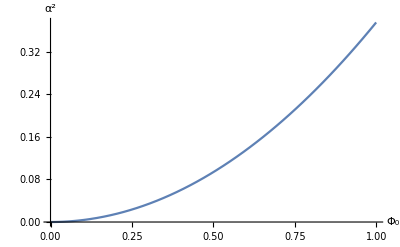

```mathematica
Plot[3/8 Φ0^2,{Φ0,0,1},AxesLabel->{"Φ_0","α^2"}]
```

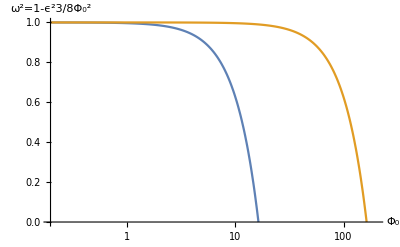

```mathematica
freq[ϵ_,Φ0_]:=√(1-ϵ^2*3/8 Φ0^2);
LogLinearPlot[{freq[0.1,Φ0]^2,freq[0.01,Φ0]^2},{Φ0,0,200},AxesLabel->{"Φ_0","ω^2=1-ϵ^23/8Φ_0^2"},PlotRange->{{0,200},{0,1}}]
```

```mathematica
Integrate[1/(Φ √(α^2-3/8 Φ^2)),Φ]
```

-ArcTanh[(√(α^2-(3 Φ^2)/8))/α]/α

## Oscillon profile

We solve for the localized oscillon profile of the type √(1-tanh(-α x))

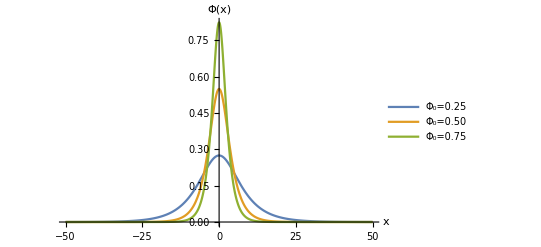

```mathematica
α[Φ0_,g_]:=√((3/8+(5 g^2)/16) Φ0^2);
Φ[Φ0_,g_,x_]:=α[Φ0,g]*√(8/3(1-Tanh[-α[Φ0,g]*x]^2));
Plot[{Φ[0.25,0.5,x],Φ[0.5,0.5,x],Φ[0.75,0.5,x]},{x,-50,50},PlotRange->All,AxesLabel->{"x","Φ(x)"},PlotLegends->{"Φ_0=0.25","Φ_0=0.50","Φ_0=0.75"}]
```

### Oscillon profile as a function of Φ_0

```mathematica
Manipulate[Plot[Φ[Φ0,0.5,x],{x,-50,50},PlotRange->All,AxesLabel->{"x","Φ(x)"}],{Φ0,0,10}]
```

### Small-amplitude solution (first order solution only)

```mathematica
freq[ϵ_,Φ0_,g_]:=√(1-ϵ^2 α[Φ0,g]^2);(*angular frequency up to third order in expansion*)
ϕ1[ϵ_,Φ0_,g_,x_,t_]:=ϵ*Φ[Φ0,g,x]*Cos[freq[ϵ,Φ0,g]*t];(*First order solution to the NLWE*)
ϵ=0.1;g=0.5;
```

```mathematica
Manipulate[Plot[{ϕ1[ϵ,0.75,g,x,t],ϕ1[ϵ,0.5,g,x,t]},{x,-50,50},PlotRange->{{-50,50},{-0.1,0.1}},AxesLabel->{"x","ϕ_(1)(t,x)"},PlotLegends->{"Φ_0=0.75","Φ_0=0.50"}],{t,0,10,0.1}]
```

```mathematica
Manipulate[Plot[0.1*Φ[20,0.5,x]*Cos[√(1-0.1^2*α[20,0.5]^2)*t],{x,-5,5},PlotRange->{{-5,5},{0,10}},AxesLabel->{"x","ϕ_(1)(t,x)"}],{t,0,10,0.1}]
```

```mathematica
Clear[g,ϵ]
```

```mathematica
DSolve[{1/12 (-4 g^2 Φ[x]^3-4 g^2 Cos[2 t] Φ[x]^3+3 Cos[3 t] Φ[x]^3-2 g^2 Cos[3 t] Φ[x]^3)==ϕ3''[t]+ϕ3[t],ϕ3[0]==0,ϕ3'[0]==0},ϕ3[t],t]
```

{{ϕ3[t]→1/288 (27 Cos[t] Φ[x]^3+46 g^2 Cos[t] Φ[x]^3-48 g^2 Cos[t]^2 Φ[x]^3-36 Cos[t]^3 Φ[x]^3+24 g^2 Cos[t]^3 Φ[x]^3-16 g^2 Cos[t] Cos[3 t] Φ[x]^3+9 Cos[t] Cos[4 t] Φ[x]^3-6 g^2 Cos[t] Cos[4 t] Φ[x]^3-144 g^2 Sin[t]^2 Φ[x]^3+18 Sin[t] Sin[2 t] Φ[x]^3-12 g^2 Sin[t] Sin[2 t] Φ[x]^3-16 g^2 Sin[t] Sin[3 t] Φ[x]^3+9 Sin[t] Sin[4 t] Φ[x]^3-6 g^2 Sin[t] Sin[4 t] Φ[x]^3)}}

```mathematica
TrigReduce[1/288 (27 Cos[t] Φ[x]^3+46 g^2 Cos[t] Φ[x]^3-48 g^2 Cos[t]^2 Φ[x]^3-36 Cos[t]^3 Φ[x]^3+24 g^2 Cos[t]^3 Φ[x]^3-16 g^2 Cos[t] Cos[3 t] Φ[x]^3+9 Cos[t] Cos[4 t] Φ[x]^3-6 g^2 Cos[t] Cos[4 t] Φ[x]^3-144 g^2 Sin[t]^2 Φ[x]^3+18 Sin[t] Sin[2 t] Φ[x]^3-12 g^2 Sin[t] Sin[2 t] Φ[x]^3-16 g^2 Sin[t] Sin[3 t] Φ[x]^3+9 Sin[t] Sin[4 t] Φ[x]^3-6 g^2 Sin[t] Sin[4 t] Φ[x]^3)]
```

1/288 (-96 g^2 Φ[x]^3+9 Cos[t] Φ[x]^3+58 g^2 Cos[t] Φ[x]^3+32 g^2 Cos[2 t] Φ[x]^3-9 Cos[3 t] Φ[x]^3+6 g^2 Cos[3 t] Φ[x]^3)